```mathematica
(*单纯的独立列表只是存储事物的一种方式，什么也做不了*)
```

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

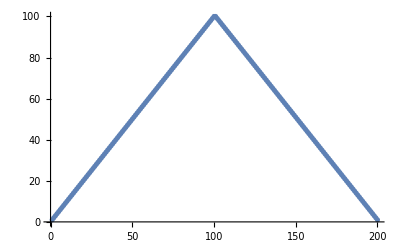

```mathematica
ListPlot[Join[Range[100],Reverse[Range[100]]]]
```

```mathematica
Range[RandomInteger[10]]
```

{1,2,3,4,5}

```mathematica
Reverse[Reverse[Range[10]]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
(*简化*)
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Join[{1,2},Join[{3,4},{5}]]
```

{1,2,3,4,5}

```mathematica
(*简化*)
Range[5]
```

{1,2,3,4,5}

```mathematica
Join[Range[10],Join[Range[10],Range[5]]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
(*简化*)
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
Reverse[Join[Range[20],Reverse[Range[20]]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

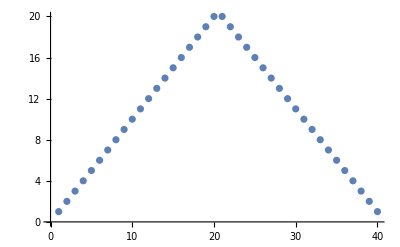

```mathematica
ListPlot[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}]
```

```mathematica
(*简化*)Join[Range[20],Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}